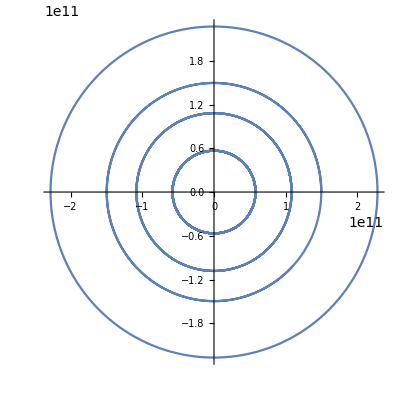

```mathematica
mercuryX[t_]=QuantityMagnitude[mercurySemiMajorAxis]*Cos[t/QuantityMagnitude[mercuryOrbitEarthYears]];
mercuryY[t_]=QuantityMagnitude[mercurySemiMinorAxis]*Sin[t/QuantityMagnitude[mercuryOrbitEarthYears]];
mercuryPlotXY=ParametricPlot[{mercuryX[t],mercuryY[t]},{t,0,marsOrbitEarthYears*2Pi}];
venusX[t_]=QuantityMagnitude[venusSemiMajorAxis]*Cos[t/QuantityMagnitude[venusOrbitEarthYears]];
venusY[t_]=QuantityMagnitude[venusSemiMinorAxis]*Sin[t/QuantityMagnitude[venusOrbitEarthYears]];
venusPlotXY=ParametricPlot[{venusX[t],venusY[t]},{t,0,marsOrbitEarthYears*2Pi}];
earthX[t_]=QuantityMagnitude[earthSemiMajorAxis]*Cos[t/QuantityMagnitude[earthOrbitEarthYears]];
earthY[t_]=QuantityMagnitude[earthSemiMinorAxis]*Sin[t/QuantityMagnitude[earthOrbitEarthYears]];
earthPlotXY=ParametricPlot[{earthX[t],earthY[t]},{t,0,marsOrbitEarthYears*2Pi}];
marsX[t_]=QuantityMagnitude[marsSemiMajorAxis]*Cos[t/QuantityMagnitude[marsOrbitEarthYears]];
marsY[t_]=QuantityMagnitude[marsSemiMinorAxis]*Sin[t/QuantityMagnitude[marsOrbitEarthYears]];
marsPlotXY=ParametricPlot[{marsX[t],marsY[t]},{t,0,marsOrbitEarthYears*2Pi}];
Show[{mercuryPlotXY,venusPlotXY,earthPlotXY,marsPlotXY},PlotRange->All]
```

```mathematica
(*Orbits when X is direction of Semi Major Axis, assuming similar centers of orbit*)
animatedMercuryOrbit=Animate[Show[mercuryPlotXY,Graphics[{PointSize[0.02],Point[{mercuryX[t],mercuryY[t]}]}]],{t,0,marsOrbitEarthYears*2Pi}];
animatedVenusOrbit=Animate[Show[venusPlotXY,Graphics[{Pink,PointSize[0.02],Point[{venusX[t],venusY[t]}]}]],{t,0,marsOrbitEarthYears*2Pi}];
animatedEarthOrbit=Animate[Show[earthPlotXY,Graphics[{Blue,PointSize[0.02],Point[{earthX[t],earthY[t]}]}]],{t,0,marsOrbitEarthYears*2Pi}];
animatedMarsOrbit=Animate[Show[marsPlotXY,Graphics[{Red,PointSize[0.02],Point[{marsX[t],marsY[t]}]}]],{t,0,marsOrbitEarthYears*2Pi}];
animatedOrbitsXY=Animate[Show[{mercuryPlotXY,Graphics[{PointSize[0.02],Point[{mercuryX[t],mercuryY[t]}]}],venusPlotXY,Graphics[{Pink,PointSize[0.02],Point[{venusX[t],venusY[t]}]}],earthPlotXY,Graphics[{Blue,PointSize[0.02],Point[{earthX[t],earthY[t]}]}],marsPlotXY,Graphics[{Red,PointSize[0.02],Point[{marsX[t],marsY[t]}]}]},PlotRange->All],{t,0,marsOrbitEarthYears*2Pi}]
animatedPlanetsXY=Animate[Show[{Graphics[{PointSize[0.02],Point[{mercuryX[t],mercuryY[t]}]}],Graphics[{Pink,PointSize[0.02],Point[{venusX[t],venusY[t]}]}],Graphics[{Blue,PointSize[0.02],Point[{earthX[t],earthY[t]}]}],Graphics[{Red,PointSize[0.02],Point[{marsX[t],marsY[t]}]}]},PlotRange->{{-QuantityMagnitude[marsSemiMajorAxis],QuantityMagnitude[marsSemiMajorAxis]},{-QuantityMagnitude[marsSemiMinorAxis],QuantityMagnitude[marsSemiMinorAxis]}},Axes->True],{t,0,marsOrbitEarthYears*2Pi}]
animatedPlanetsXYFunny=Animate[Show[{Graphics[{PointSize[0.02],Point[{mercuryX[t],mercuryY[t]}]}],Graphics[{Pink,PointSize[0.02],Point[{venusX[t],venusY[t]}]}],Graphics[{Blue,PointSize[0.02],Point[{earthX[t],earthY[t]}]}],Graphics[{Red,PointSize[0.02],Point[{marsX[t],marsY[t]}]}]}],{t,0,marsOrbitEarthYears*2Pi}]
```

```mathematica
(*Orbits when z tilt happens only in the y direction, and X is still direction of Major Axis*)
mercuryX3D[t_]=QuantityMagnitude[mercurySemiMajorAxis]*Cos[t/QuantityMagnitude[mercuryOrbitEarthYears]];
mercuryY3D[t_]=QuantityMagnitude[mercurySemiMinorAxis]*Sin[t/QuantityMagnitude[mercuryOrbitEarthYears]]*Cos[QuantityMagnitude[mercuryInclination]*Degree];
mercuryZ3D[t_]=QuantityMagnitude[mercurySemiMinorAxis]*Sin[t/QuantityMagnitude[mercuryOrbitEarthYears]]*Sin[QuantityMagnitude[mercuryInclination]*Degree];
mercuryPlotXYZ=ParametricPlot3D[{mercuryX3D[t],mercuryY3D[t],mercuryZ3D[t]},{t,0,2Pi*marsOrbitEarthYears}];
(*First Program test*)
animatedMercury3DTest=Animate[Show[{mercuryPlotXYZ,Graphics3D[{Gray, PointSize[0.03],Point[{mercuryX3D[t],mercuryY3D[t],mercuryZ3D[t]}]}]},PlotRange->All],{t,0,2*Pi*QuantityMagnitude[marsOrbitEarthYears]}]
(*Full parametric Plots*)
venusX3D[t_]=QuantityMagnitude[venusSemiMajorAxis]*Cos[t/QuantityMagnitude[venusOrbitEarthYears]];
venusY3D[t_]=QuantityMagnitude[venusSemiMinorAxis]*Sin[t/QuantityMagnitude[venusOrbitEarthYears]]*Cos[QuantityMagnitude[venusInclination]*Degree];
venusZ3D[t_]=QuantityMagnitude[venusSemiMinorAxis]*Sin[t/QuantityMagnitude[venusOrbitEarthYears]]*Sin[QuantityMagnitude[venusInclination]*Degree];
venusPlotXYZ=ParametricPlot3D[{venusX3D[t],venusY3D[t],venusZ3D[t]},{t,0,2Pi*marsOrbitEarthYears}];
earthX3D[t_]=QuantityMagnitude[earthSemiMajorAxis]*Cos[t/QuantityMagnitude[earthOrbitEarthYears]];
earthY3D[t_]=QuantityMagnitude[earthSemiMinorAxis]*Sin[t/QuantityMagnitude[earthOrbitEarthYears]]*Cos[QuantityMagnitude[earthInclination]*Degree];
earthZ3D[t_]=QuantityMagnitude[earthSemiMinorAxis]*Sin[t/QuantityMagnitude[earthOrbitEarthYears]]*Sin[QuantityMagnitude[earthInclination]*Degree];
earthPlotXYZ=ParametricPlot3D[{earthX3D[t],earthY3D[t],earthZ3D[t]},{t,0,2Pi*marsOrbitEarthYears}];
marsX3D[t_]=QuantityMagnitude[marsSemiMajorAxis]*Cos[t/QuantityMagnitude[marsOrbitEarthYears]];
marsY3D[t_]=QuantityMagnitude[marsSemiMinorAxis]*Sin[t/QuantityMagnitude[marsOrbitEarthYears]]*Cos[QuantityMagnitude[marsInclination]*Degree];
marsZ3D[t_]=QuantityMagnitude[marsSemiMinorAxis]*Sin[t/QuantityMagnitude[marsOrbitEarthYears]]*Sin[QuantityMagnitude[marsInclination]*Degree];
marsPlotXYZ=ParametricPlot3D[{marsX3D[t],marsY3D[t],marsZ3D[t]},{t,0,2Pi*marsOrbitEarthYears}];
(*Final Program Test*)
animatedAllOrbits3DTest=Animate[Show[{mercuryPlotXYZ,venusPlotXYZ,earthPlotXYZ,marsPlotXYZ,Graphics3D[{{Gray, PointSize[0.03],Point[{mercuryX3D[t],mercuryY3D[t],mercuryZ3D[t]}]},{Pink,PointSize[0.03],Point[{venusX3D[t],venusY3D[t],venusZ3D[t]}]},{Blue,PointSize[0.03],Point[{earthX3D[t],earthY3D[t],earthZ3D[t]}]},{Red,PointSize[0.03],Point[{marsX3D[t],marsY3D[t],marsZ3D[t]}]}}]},PlotRange->All],{t,0,2*Pi*marsOrbitEarthYears}]
animatedAllPlanets3DTestFunny=Animate[Show[{Graphics3D[{{Gray, PointSize[0.03],Point[{mercuryX3D[t],mercuryY3D[t],mercuryZ3D[t]}]},{Pink,PointSize[0.03],Point[{venusX3D[t],venusY3D[t],venusZ3D[t]}]},{Blue,PointSize[0.03],Point[{earthX3D[t],earthY3D[t],earthZ3D[t]}]},{Red,PointSize[0.03],Point[{marsX3D[t],marsY3D[t],marsZ3D[t]}]}}]},PlotRange->All],{t,0,2*Pi*marsOrbitEarthYears}]
animatedAllPlanets3DTest=Animate[Show[{Graphics3D[{{Gray, PointSize[0.03],Point[{mercuryX3D[t],mercuryY3D[t],mercuryZ3D[t]}]},{Pink,PointSize[0.03],Point[{venusX3D[t],venusY3D[t],venusZ3D[t]}]},{Blue,PointSize[0.03],Point[{earthX3D[t],earthY3D[t],earthZ3D[t]}]},{Red,PointSize[0.03],Point[{marsX3D[t],marsY3D[t],marsZ3D[t]}]}}]},PlotRange->{{-QuantityMagnitude[marsSemiMajorAxis],QuantityMagnitude[marsSemiMajorAxis]},{-QuantityMagnitude[marsSemiMinorAxis],QuantityMagnitude[marsSemiMinorAxis]},{-10*^9,10*^9}}],{t,0,2*Pi*marsOrbitEarthYears}]
```

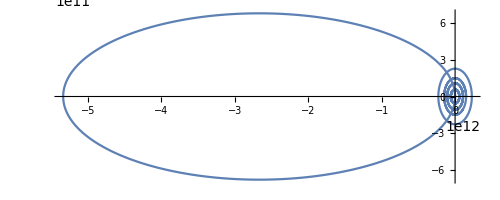

```mathematica
(*Comet in XY Plane*)
halleysSemiMajor=AstronomicalData["Comet1PHalley","SemimajorAxis"];
halleysSemiMinor=Sqrt[halleysSemiMajor^2(1-AstronomicalData["Comet1PHalley","Eccentricity"]^2)];
halleysOrbitPeriod=AstronomicalData["Comet1PHalley","OrbitPeriod"];
halleysOffCenter=(35.082+0.586)*1.496*^11/2;
halleysOrbitEarthYears=halleysOrbitPeriod/earthOrbitPeriod;
halleysCometX[t_]=QuantityMagnitude[halleysSemiMajor]*Cos[t/QuantityMagnitude[halleysOrbitEarthYears]]-halleysOffCenter;
halleysCometY[t_]=QuantityMagnitude[halleysSemiMinor]*Sin[t/QuantityMagnitude[halleysOrbitEarthYears]];
halleysCometPlotXY=ParametricPlot[{halleysCometX[t],halleysCometY[t]},{t,0,2Pi*halleysOrbitEarthYears},PlotRange->All];
Show[{mercuryPlotXY,venusPlotXY,earthPlotXY,marsPlotXY,halleysCometPlotXY},PlotRange->All]
```

```mathematica
animatedOrbitsCometXY=Animate[Show[{mercuryPlotXY,Graphics[{PointSize[0.02],Point[{mercuryX[t],mercuryY[t]}]}],venusPlotXY,Graphics[{Pink,PointSize[0.02],Point[{venusX[t],venusY[t]}]}],earthPlotXY,Graphics[{Blue,PointSize[0.02],Point[{earthX[t],earthY[t]}]}],marsPlotXY,Graphics[{Red,PointSize[0.02],Point[{marsX[t],marsY[t]}]}],halleysCometPlotXY,Graphics[{Green,PointSize[0.03],Point[{halleysCometX[t],halleysCometY[t]}]}]},PlotRange->All],{t,0,halleysOrbitEarthYears*2Pi}]
```